```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Transforms

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Three common “kinds” of functions in image processing are transforms, filters, and spatial mappings. Filters change the value of the pixels based on the values of all the pixels in a local neighborhood, spatial mappings leave the values of the pixels intact (more or less) but move them from one spatial location to another, and transforms calculate the values of each output pixel using the complete image. There are a number of classical transforms that are used extensively in image processing and also several transforms that are (more or less) unique to image processing. This notebook briefly describes the Fourier Transform and its Wavelet cousin, the Radon transform and the distance transform.

```mathematica
TableForm[{{Hyperlink["SpecXRay",{"visualVocabTransforms.nb","labelSpecXRay"}],labelSpecXRay},{Hyperlink["WaveletTransform",{"visualVocabTransforms.nb","labelWaveletTransform"}],labelWaveletTransform},{Hyperlink["RadonTransform",{"visualVocabTransforms.nb","labelRadonTransform"}],labelRadonTransform},{Hyperlink["DistanceTransform",{"visualVocabTransforms.nb","labelDistanceTransform"}],labelDistanceTransform}}]
```

| Fourier transform (spectrum) of the image
 | Wavelet transforms decompose an image using shifted and scaled versions of a mother wavelet
 | The Radon transform can be used to locate the orientation of an image
 | The distance transform can be used to segment images and
to find the skeleton (the connected inner core) of a shape

### Fourier Transforms

By far the most common of the transforms, and also most useful because of its deep connections with linear systems and filters, is the Fourier transform. When a Fourier transform is applied to a signal, the output is called the spectrum, and it represents how the signal may be decomposed into (and rebuilt from) a collection of sinusoids. For example, here is the sound of a small Indonesian gong (press the small play button to hear the sound).

```mathematica
gong = -Graphics-;
```

The data in the sound file is plotted with time on the horizontal axis and amplitude on the vertical axis. This shows how the sound evolves over time. The spectrum plots frequency on the horizontal axis and magnitude on the vertical. This shows what the sound consists of: in this case, there are three main sinusoidal components (shown here with both positive and negative frequency components) at three frequencies, at about 520, 630, and 660 Hz. Physically, these represent the three largest resonant modes of the vibrating metallic surface of the gong. This example is carried out in detail in Using the DFT.

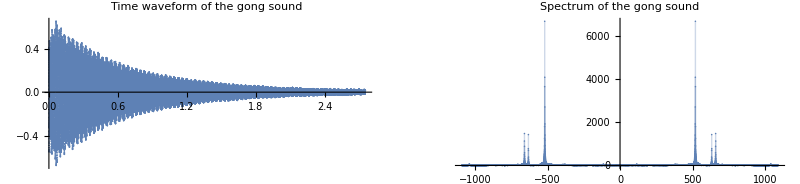

```mathematica
gongData=Flatten[gong[[1,1]]];
gongTs=1./gong[[1,2]];
numSam=Length[gongData];
timeAxis=gongTs Range[1,numSam];
numSam=Length[gongData];
freqInd=1/(gongTs numSam);
fftGongData=RotateLeft[Fourier[gongData,FourierParameters->{1,-1}],Round[numSam/2]];
ssf=freqInd Range[-numSam/2,numSam/2-1];
mid=Ceiling[numSam/2];z=3000;
GraphicsRow[{ListPlot[Transpose[{timeAxis,gongData}],PlotRange->All,PlotLabel->"Time waveform of the gong sound"]
,ListPlot[Transpose[{ssf[[mid-z;;mid+z]],Abs[fftGongData[[mid-z;;mid+z]]]}],AspectRatio->1/3,PlotRange->All,Filling->Axis,PlotLabel->"Spectrum of the gong sound"]},ImageSize->800]
```

Of course Fourier methods work similarly in two (and more) dimensions. With images, the Fourier spectrum represents a decomposition spatial sine waves (for instance, undulations in grayscale value across the surface of an image). An example, pursued in more detail in the notebook on thread counting via Fourier methods, shows a patch of a canvas x-ray and its spectrum. The shapes and locations of the dark spots in the spectrum show the frequencies of the sinusoids that best correlate with the image. In this case, because the image has repetitive patterns, the strong sinusoidal components are related to the weave patterns, as we will see.

```mathematica
labelSpecXRay="Fourier transform (spectrum) of the image";
infoSpecXRay="This is the spectrum of a thread image.\n\nZoom in/out to see the spectrum more closely.\n\nUse the offset controller to move around in the spectrum.\n\nUse the mesh to help count.\n\nYou can see there are four large black spots in a rough cross shape. These are the peaks of the spectrum in the x and y directions (in this representation, black is large and white is small).\n\nCount how many pixels over from the center the peak to the right is. This is proportional to the dominant frequency in the x-direction and hence to the thread count in the horizontal direction. (Answer: about 23 pixels over, corresponding to 23 vertical threads in the image).\n\nCount how many pixels up from the center the vertical black spot is. How many horizontal theads are in the image, according to this estimate?";
im=ImageData[img=allImagesXray[[f634Tile]]];
xf=Abs[Fourier[im-Mean[im],FourierParameters->{1,-1}]];
{d1,d2}=Ceiling[Dimensions[xf]/2];
xCentered1=RotateLeft[xf,{d1,d2}];
Row[{Image[img,ImageSize->300],Spacer[40],Manipulate[ArrayPlot[xCentered1,PlotRange->{{d1-zoom,d1+zoom}+offset[[2]],{d2-zoom,d2+zoom}-offset[[1]]},Frame->True,FrameLabel->{"rows of FFT matrix","columns of FFT matrix"},FrameTicks->{{d1,None},{d2,None}},Mesh->mesh,MeshStyle->Opacity[0.1],ImageSize->{400,400}],
Row[{Control[{{zoom,40},100,3,-1}],Spacer[20],Control[{mesh,{False,True}}],Spacer[20],info[infoSpecXRay]}],{{offset,{0,0}},{-38,-38},{38,38}},FrameLabel->Style[labelSpecXRay,Medium],TrackedSymbols->{zoom,mesh,offset},SaveDefinitions->True]}]
```

-Graphics-

What’s so special about sinusoids? Three things. First, they are a basic representation of oscillatory and/or motion periodic motion, as suggested above by the gong and the canvas image. Second, they can be used for designing linear filters, a topic that is explored in depth in the notebook on linear filtering. Third, they can be used to help design and understand the operation of any linear filter, which is discussed in some detail in the notebook on Fourier transforms.

### Wavelet Transforms

What's so special about sinusoids? Nothing! In the same way that Fourier methods rely on properties of the sinusoid to decompose and filter signals, wavelet transforms use time-limited undulating waveforms to decompose the signal into time and scale. This can be useful when filtering or smoothing images where the noise is nonstationary (i.e., where the noise is fundamentally different in different segments of the image) and as a way of searching for components or features that have a specific scale (size) within the image. Several more examples of the uses of wavelet transforms appear here.

```mathematica
labelWaveletTransform="Wavelet transforms decompose an image using shifted and scaled versions of a mother wavelet";
infoWaveletTransform="Instead of decomposing an image using sinusoids (like the Fourier transform) wavelet transforms use a collection of scaled functions. At each refinement level (chosen using the left hand slider) there are a number of images which successively approximate and refine the image.\n\nWith the refinement level set to 3, there are 12 images. The right hand slider chooses which of these images to enlarge.\n\nDifferent mother wavelets can be chosen from the pulldown menu.\n\nObserve how some of the wavelet images have a lowpass blurring kind of character, some have a highpass edge-effect character, and many (especially at higher levels) are blocky.";
Manipulate[If[j>4 n,j=4 n];
Row[{WaveletImagePlot[dw=DiscreteWaveletTransform[ImageResize[allImagesColor[[i]],{400}],waveletType,n],ImageSize->80,PlotLayout->"Grid"],dw[All,"Image"][[j,1]],Image[dw[All,"Image"][[j,2]],ImageSize->350]}],Row[{Control[{{i,vanBedroom,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],Control[{{waveletType,HaarWavelet[],"mother wavelet"},{HaarWavelet[],DaubechiesWavelet[2],DaubechiesWavelet[4],SymletWavelet[2],BattleLemarieWavelet[3],BiorthogonalSplineWavelet[4,2],BattleLemarieWavelet[3]}}],Spacer[20],info[infoWaveletTransform]}],Row[{Control[{{n,3,"scale (refinement)"},1,7,1,Appearance->"Labeled"}],Spacer[20],Control[{{j,1,"component to enlarge"},1,Dynamic[4 n],1,Appearance->"Labeled"}]}],FrameLabel->Style[labelWaveletTransform,Medium],TrackedSymbols->{i,j,n,waveletType},SaveDefinitions->saveDef]
```

### The Radon Transform

Imagine shining a light bright enough to pierce through an object; the amount of light that reaches the other side is inversely proportional to the amount of matter in the path. The Radon Transform projects through an image (like shining a light) at all possible angles. For angles where all the pixel values are small, the output is small; for angles where there are many large pixel values, the output of the transform is large. This can be used to locate lines in an image and hence the orientation or rotation of an image such as thread x-rays. In this example, a circular section of an x-ray canvas is binarized (using the threshold value on the slider) and then the Radon transform is shown on the right. The wrinkly vertical slices near the middle and near the right hand edge correspond to the vertical and horizontal stripes in the image. The meaning of the various features in the transform are discussed in detail in the notebook on the Radon transform and the method can be applied to the problem of calculating angle maps.

```mathematica
labelRadonTransform="The Radon transform can be used to locate the orientation of an image";
infoRadonTransform="An x-ray image (left) is binarized (middle) and Radon tranformed (right).\n\nThe columns of the Radon transform indicate slope, and the columns with the greatest variation (there are two: one at the right edge and one near the middle) show the angle of the vertical and horizontal threads.\n\nChange the threshold of the binarization to most clearly show the vertical stripes.\n\nEven in images where the individual threads are hard to see, the locations of greatest variation in the Radon transform are often clear.\n\nLook at L17, you can see the weave pattern just starting to appear at a threshold of about 0.7. At the same time, the wrinkles in the Radon trasnform begin to appear.\n\nNow look at F458Diag36, adjust the threshold, and count the number of dimples in the center column and the right column, now count the threads in the vertical and horizontal directions. What can you conclude?\n\nDo you find it easier to count the dimples when looking at the negative x-rays or the positive?";
Manipulate[If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
radImg=ImageAdjust[Radon[binImg=Binarize[img=ImageMultiply[whiteDisk,ImageTake[img,{1,200},{1,200}]],s]]];
GraphicsRow[{img,binImg,radImg},ImageSize->800],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],Control[{{s,0.5,"threshold"},0,1}],Spacer[20],info[infoRadonTransform]}],SynchronousUpdating->False,
FrameLabel->Style[labelRadonTransform,Medium],TrackedSymbols->{i,s,invert},SaveDefinitions->saveDef]
```

### The Distance Transform

The distance transform replaces each pixel of an image by its distance from a specified set S. While this is done numerically in the transform, it is easy to visualize the answer for simple shapes: the further from the set boundary, the whiter the image. Here are a number of examples:

```mathematica
labelDistanceTransform="The distance transform can be used to segment images and\nto find the skeleton (the connected inner core) of a shape";
infoDistanceTransform="For simple shapes, the distance transform has a simple intrepretation: the further from a boundary a point is, the whiter the point. In the first image, the brightest spot is the one furthest from the border, which is at the center of the largest triangular shape.";
Manipulate[ImageAdjust[Image[DistanceTransform[ColorNegate[shapes[[i]]]],ImageSize->{300}]],Row[{Control[{{i,1,"image"},Thread[Range[Length[shapes]]->shapes],ControlType->PopupMenu}],Spacer[20],info[infoDistanceTransform]}],FrameLabel->Style[labelDistanceTransform,Medium],TrackedSymbols->{i},SaveDefinitions->True]
```

Further examples of the Distance transform appear here.